# Video Flashing Reduction

Author : Apple Inc.

Version : 1.0

## Introduction

This notebook implements the Video Flashing Reduction algorithm. It reads a video file and exports a mitigated video file. It also returns an association that contains intermediate products of the algorithm. The main function is VideoFlashingReduction. Brief documentation is provided for that and the other functions. An example of usage is given below.

## Initialization

```mathematica
SetDirectory[NotebookDirectory[]]
```

## Functions

#### VideoFlashingReduction

```mathematica
VideoFlashingReduction::usage = "VideoFlashingReduction[file_,options___Rule] Apply the Video Flashing Reduction algorithm to a short video clip. The function returns an Association with a number of intermediate calculations. The mitigated video is exported as a file mitigated.mp4.
Options:
\"Nits\"->500 Peak luminance of the display
\"Area\"->(45^2/1.6) Area of the display (degrees^2)
\"FilterGain\"->1 Global filter gain
\"EnergyPoolGammaScale\"->0.15 Scale parameter of the energy kernel (seconds)
\"EnergyPoolGammaShape\"->2 Shape parameter of the energy kernel
\"EnergyPoolExponent\"->2 Exponent for calculation of energy
\"RiskMapShape\"->3 Shape parameter of the risk mapping function
\"RiskMapScale\"->200 Scale parameter of the risk mapping function
\"RiskMapOffset\"->33 Offset parameter of the risk mapping function
\"MitigationWeights\"->{1,0} Luminance and contrast mitigation weights, each 0-1
\"MitigationGain\"-> 1 Overall gain of mitigation, 0-1
\"RiskThreshold\"->1.8 Threshold for step masking
\"TauMitigation\"->2 Time constant for mitigation fading (seconds)
\"TauAdapt\"->1 Time constant for light adaptation (seconds)
\"OutputFileName\"->\"mitigated.mp4\" filename of the exported mitigated video, False for no export.

 ";
```

```mathematica
Options[VideoFlashingReduction]={"Nits"->500,"Area"->(45^2/1.6),"Verbose"->False,"FilterGain"->1,"Kernels":>UFMKernels03,"EnergyPoolGammaScale"->0.15,"EnergyPoolGammaShape"->2,"EnergyPoolExponent"->2,"RiskMapShape"->3,"RiskMapScale"->200,"RiskMapOffset"->33
,"MitigationWeights"->{1,0},"MitigationGain"-> 1,"RiskThreshold"->1.8,"TauMitigation"->2,"TauAdapt"->1,"OutputFileName"->"mitigated.mp4"};
```

```mathematica
Clear[VideoFlashingReduction]
```

```mathematica
VideoFlashingReduction[file_,options___Rule] := Block[{
muAdapt,tauAdapt,numFrames,vidFrameRate,kernels,nits,area,verbose,gain,frames,standardSizes,standardNits,logStandardNits,standardFrameRates,kernelSize,equivalentSize,kernelFrameRate,contrastKernels,contrastKernelLengths,luminance,adaptationLevel,energyExponent,energyGammaScale,energygammashape ,energyKernel ,responseAdjust,response,responses,energy,contrast,cA,riskmapshape,riskmapscale,riskmapoffset,risk,mitigationGain ,mitigationWeights,contrastFactor,luminanceFactor,contrastKernelEnergies,mitigated,energies,mitigationStrength,mitigationStrengthOld,MuMitigation,riskThreshold,tauMitigation,contrastEnergies,correlations,iota,normalizedCorrelations,correlationEnergies,correlationEnergy,tmp,outputFileName},

(* Set options *)
{kernels,nits,area,gain,energyExponent,energyGammaScale,energygammashape,riskmapshape,riskmapscale,riskmapoffset,mitigationGain,mitigationWeights,riskThreshold,tauMitigation,tauAdapt,outputFileName} = {"Kernels","Nits","Area","FilterGain","EnergyPoolExponent","EnergyPoolGammaScale","EnergyPoolGammaShape","RiskMapShape","RiskMapScale","RiskMapOffset","MitigationGain","MitigationWeights","RiskThreshold","TauMitigation","TauAdapt","OutputFileName"} /. {options} /. Options[VideoFlashingReduction];

(* Read video *)
frames =VideoFrameList[Video[file],All];
vidFrameRate=QuantityMagnitude[Import[file,"FrameRate"]];
numFrames = QuantityMagnitude[Import[file,"FrameCount"]];

 (* Define standard sizes, nits, rates *)
standardSizes = {6,20,45};
standardNits = {0.2,1,10,150,500};
logStandardNits = Log10[standardNits]//N;
standardFrameRates = {24,25,30,50,60,90,120};

(* Select kernels *)
equivalentSize = Sqrt[area 1.6];
kernelSize = Nearest[standardSizes,equivalentSize,1][[1]];
kernelFrameRate = Nearest[standardFrameRates,vidFrameRate,1][[1]];
contrastKernels=kernels[[IndexOf[standardSizes,kernelSize],All,IndexOf[standardFrameRates,kernelFrameRate]]];
contrastKernelLengths = Length /@contrastKernels;
contrastKernelEnergies = Total /@ (contrastKernels^energyExponent);
energyKernel = Rest@GammaKernel[vidFrameRate,energygammashape,energyGammaScale,0.991];

(* Constants and derived quantities *)
cA = 0.263; (* Area scale for PoV *)
muAdapt = 1.-Exp[-1/(tauAdapt vidFrameRate)];
MuMitigation= 1.-Exp[-1/(tauMitigation vidFrameRate)];
responseAdjust =((equivalentSize/kernelSize)^(2 cA))(gain /vidFrameRate^(1/energyExponent));

(* Analyze frames *)
luminance=nits (MeanNormalizedLuminance /@ frames);
adaptationLevel = ExponentialMovingAverage[luminance,muAdapt];
contrast = (luminance/adaptationLevel)-1;
responses=ListConvolve[#,contrast,1,0]& /@ contrastKernels;
energies=(ListConvolve[energyKernel,#,1,0]& /@ (responses^energyExponent))^(1/energyExponent);
energy=MapThread[InterpolateEnergy[#1,logStandardNits,#2]& ,{Log10[adaptationLevel], Transpose[energies]}];
energy *= responseAdjust;
risk = RiskMap[#,riskmapshape,riskmapscale,riskmapoffset]& /@ energy;

(* Step masking *)
contrastEnergies=(# MovingAverage[PadLeft[contrast^2,numFrames+#-1,0],#])& /@ contrastKernelLengths;
correlations=ListCorrelate[#,contrast,-1,0]& /@ contrastKernels;
iota = .000001;
normalizedCorrelations = correlations/((iota +contrastEnergies contrastKernelEnergies)^(1/energyExponent));
correlationEnergies=(ListConvolve[energyKernel,#,1,0]& /@ (normalizedCorrelations^energyExponent))^(1/energyExponent);
correlationEnergy=MapThread[InterpolateEnergy[#1,logStandardNits,#2]& ,{Log10[adaptationLevel], Transpose[correlationEnergies]}];
risk = MapThread[If[#1<riskThreshold, 0,#2 ]& ,{ correlationEnergy,risk}]; 

(* Mitigation *)
mitigationStrength=mitigationGain Log10[Clip[risk,{1,100}]]/2.;
mitigationStrengthOld=0;
mitigationStrength=If[ #< mitigationStrengthOld,(tmp = # MuMitigation + mitigationStrengthOld (1 - MuMitigation);
If[tmp<.01,tmp=0];
mitigationStrengthOld=tmp;
tmp),(mitigationStrengthOld=#;#)]&  /@  mitigationStrength;
{contrastFactor,luminanceFactor}= 1-((# mitigationStrength )& /@ mitigationWeights);
mitigated= MapThread[Mitigate,{frames,contrastFactor,luminanceFactor,adaptationLevel/nits}];

(* Export mitigated video *)
If[StringQ[outputFileName],Export[outputFileName,mitigated,FrameRate->vidFrameRate]];

(* Return interesting quantities *)
AssociationThread[{"vidFrameRate","kernelFrameRate","luminance","adaptationLevel","contrast","energy","risk","correlationEnergy","energies","responses","energyKernel","mitigationStrength","contrastKernels","normalizedCorrelations"},{vidFrameRate,kernelFrameRate,luminance,adaptationLevel,contrast,energy,risk,correlationEnergy,energies,responses,energyKernel,mitigationStrength,contrastKernels,normalizedCorrelations}]
]
```

#### MeanNormalizedLuminance

```mathematica
MeanNormalizedLuminance::usage = "MeanNormalizedLuminance[image_] Compute the mean normalized luminance from a color image.";
```

```mathematica
MeanNormalizedLuminance[image_] := 
Mean[ColorSeparate[ColorConvert[If[ImageChannels[image]==4,RemoveAlphaChannel[image],image],"XYZ"]][[2]]]
```

#### InterpolateEnergy

```mathematica
InterpolateEnergy::usage = "InterpolateEnergy[logNits_,logStandardNits_,energies_] Interpolate a single energy value from the five energies, based on the current adaptation level and the five standard log luminances of the kernels.";
```

```mathematica
InterpolateEnergy[logNits_,logStandardNits_,energies_] :=Piecewise[{
{energies[[1]],logNits<logStandardNits[[1]]}
,{energies[[1]]+ (logNits-logStandardNits[[1]])(energies[[2]]-energies[[1]])/(logStandardNits[[2]]-logStandardNits[[1]]),logNits<logStandardNits[[2]]}
,{energies[[2]]+ (logNits-logStandardNits[[2]])(energies[[3]]-energies[[2]])/(logStandardNits[[3]]-logStandardNits[[2]]),logNits<logStandardNits[[3]]}
,{energies[[3]]+ (logNits-logStandardNits[[3]])(energies[[4]]-energies[[3]])/(logStandardNits[[4]]-logStandardNits[[3]]),logNits<logStandardNits[[4]]}
,{energies[[4]]+ (logNits-logStandardNits[[4]])(energies[[5]]-energies[[4]])/(logStandardNits[[5]]-logStandardNits[[4]]),logNits<logStandardNits[[5]]}
},energies[[5]]]
```

#### RiskMap

```mathematica
RiskMap::usage = "RiskMap[energy_,shape_,scale_,offset_] Map the energy into a risk. The parameters are shape, scale and offset.";
```

```mathematica
RiskMap[energy_,shape_,scale_,offset_] := If[energy<offset,0,100 (1-ⅇ^(-((energy-offset)/scale)^shape))]
```

#### Mitigate

```mathematica
Mitigate::usage = "Mitigate[input_,contrastfactor_,lumfactor_,arlum_] Reduce the contrast and/or luminance of an image by factors (0-1) where 1 means no change. The result is lumfactor (arlum-arlum contrastfactor+contrastfactor input). The result is clipped to {0,1}. The input can be an image, a relative luminance, or a list of relative luminances. arlum is either a single adapting relative luminance, or a list of length equal to the input.";
```

```mathematica
Mitigate[image_Image,contrastfactor_,lumfactor_,arlum_] := Block[{gamma=2.2,rlum,gain,offset},
rlum= ImageData[image]^gamma;
gain = contrastfactor lumfactor;
offset = (1-contrastfactor) lumfactor  arlum;
Image[Clip[gain rlum + offset,{0,1}]^(1/gamma),Options[image]]
]
```

#### GammaKernel

```mathematica
GammaKernel::usage = "GammaKernel[w_,shape_,scale_,quantile_:0.99]. Compute a kernel that is sampled at rate w (Hz) from a Gamma PDF with paramaters shape and scale. The argument quantile specifies what quantile of the distribution should be included. ";
```

```mathematica
GammaKernel[w_,shape_,scale_,quantile_:0.99] := Block[{dist,argmax,tmax},
dist = GammaDistribution[shape,scale];
tmax=Quantile[dist,quantile];
PDF[dist,Range[0,tmax+1/w,1/w]]
]
```

#### IndexOf

```mathematica
IndexOf::usage = "IndexOf[list_,item_] Return the index of the item in the list.";
```

```mathematica
IndexOf[list_,item_] := Position[list,item][[1,1]]
```

## Kernels

```mathematica
UFMKernels03::usage="An array of filter kernels based on the Universal Flicker Metric. The dimensions of the array are {3, 5, 7}, corresponding to the standard sizes, standard luminances, and standard frame rates.";
```

```mathematica
UFMKernels03={{{{16.71817198509924,37.7068247160281,-33.40149682031351,-24.632145197796774,-0.38647089073704033},{46.90648095320929,-0.2783003114525284,-31.359460240507502,-11.151360698143074,-0.4410315788229566},{4.874872123894335,39.68876196405938,4.601124602820024,-29.597722947856745,-17.0841714460608,-3.986193783586406,-0.4994842991751935,-0.03975104977147303},{0.3827336658504792,11.600592592584302,25.926341747138856,16.171444743032666,-4.071929807082321,-15.789140152149065,-15.459850353221718,-9.715645424431317,-4.578716201487029,-1.7376284698711058,-0.5549903887091708,-0.15387419364826427,-0.037895753778999834},{0,0.4802136705750231,6.921584852329777,19.05440083711387,20.097901494730333,8.063161384574201,-5.654891847393663,-13.177975787169684,-13.542034950335001,-9.90883878417787,-5.753277628650484,-2.789896929356679,-1.167391486077913,-0.43162765539701115,-0.14362424574074667,-0.043643447843307634,-0.012255914614523545},{0,0,0.02542307453074896,0.5148531514769089,3.0587391267160515,8.361132695855487,13.333054824532386,14.125431697636476,10.316963858522698,4.169591743341239,-1.9595046088224652,-6.610801790734411,-9.12081474097618,-9.497661239536212,-8.300467620008149,-6.339777008663937,-4.327111321072084,-2.679655089689874,-1.5232995603283963,-0.8024947180607245,-0.394919931337837,-0.18278386460087911,-0.08003421925639816,-0.03332257902010153,-0.013251567033012333},{-0.033983459186743295,-0.018342069019434287,0,0.04142073998615343,0.3812605526743317,1.582273272508688,4.044248079246128,7.264314062038102,9.934484165247886,10.858633310633376,9.678127344686978,6.859568912853607,3.2425268301249663,-0.37349999157438135,-3.4182661903066256,-5.578013053407784,-6.761704544125862,-7.051814021835941,-6.64593432693529,-5.792363015204131,-4.7312225035033215,-3.6537633966395155,-2.685178882846643,-1.887521932205223,-1.2744702546931388,-0.8295553252909336,-0.522144960243991,-0.31868012975996873,-0.1890560372282894,-0.10925423551671858}},{{100.23732878107762,-0.8570770621676594,-63.966083344356505,-19.96448955893178,-0.6662960967103904},{96.98800634197241,4.48142963749884,-63.553532418891805,-24.106361420485932,-1.8545472064088004,-0.049874055047917386},{9.559429399551036,83.99168532406833,17.931446405015162,-55.198745060844026,-36.01713423527094,-9.161688185521802,-1.2159214108525065,-0.10044277993263702},{0.03334878355746808,9.408633265982841,47.18905525185455,43.213403403649,3.8203808625875912,-27.065115212313817,-35.95078519716568,-27.301732131650674,-14.56983458885805,-5.9570753466386455,-1.9727942061582635,-0.5508216238175149,-0.1336329675269811,-0.028832803241512238},{0,0.35056623364369577,11.367555467652776,39.30977665891702,39.391051894517034,14.283919647694407,-10.213467933842914,-27.07740903710374,-31.17629727706288,-23.745862165842333,-13.214956404895691,-5.698052675391537,-1.9869209533340542,-0.5791412416883598,-0.14484038748972178,-0.03174165323791112},{0.0671107933368082,3.1780473089217196,15.065898482772218,27.822113436515913,30.502333707859297,23.335404002420365,11.921736354572463,0.30551546830675763,-9.434449753336299,-15.927694076468262,-18.496507745162365,-17.557643661606836,-14.403386064022621,-10.506042483639735,-6.9411176043102305,-4.210728754716575,-2.370657739888276,-1.2495029563618223,-0.6210010293149386,-0.2927982337995886,-0.13164618919793797,-0.05669417365992418,-0.023476156525715372},{-0.030040768673748764,-0.014632526714151911,0,0.1572031334579378,1.3716196759056354,5.409177046774954,12.478369967165058,19.44354822414024,22.405208190214157,20.176733397272475,14.40610260124229,7.415374271082862,0.6815097034988756,-5.204010797740744,-9.97138975933128,-13.344113098281195,-15.089984608538398,-15.197098830187125,-13.943021945590088,-11.80914175627919,-9.320077825179304,-6.905326149317534,-4.8328565349242245,-3.212084212929824,-2.0367683646762273,-1.2371753801194048,-0.7224598220152298,-0.40688569793948154,-0.22163655302055482,-0.11706454578813164}},{{192.75116398979185,-104.15161933445161,-68.62652169101163,-1.1449901457615466},{178.34129173567973,-117.4806926273474,-80.75940446737351,-0.6951706008209865},{175.69051402033062,-76.82421292812386,-106.41612553802918,-14.744360139875422,-0.10665301834013836},{0.6746854234503256,53.91259328166806,133.94911891514005,-4.7566379538085215,-87.25292763561845,-53.432595755087426,-17.515273101384693,-3.9907158768537108,-0.7082924965190901,-0.10448802269034588,-0.013356014563023775},{0.7600969496243912,71.06124717441166,113.92422224176826,7.184777011299212,-58.535860071970006,-59.829830169828554,-34.17654587012664,-13.595823953615392,-4.174741651610631,-1.0565233988865714,-0.2304983708494059,-0.044754858508033415},{0.03063254482539688,6.7186168181093375,46.51020612406365,76.53219443017332,49.27024258534835,-1.3965031961236132,-37.701174047637124,-49.65539196201734,-43.72483046323303,-30.65855515717136,-18.2568682546217,-9.573981901822654,-4.531681193356933,-1.9717357566023892,-0.7997599931230713,-0.30576961638430955,-0.1111710637278542,-0.03871309939472832,-0.012987670706400542},{0,0,0.5029144163784453,7.04812004848818,28.956629967560612,54.519708213334106,58.81226127943772,38.87912929388627,10.326723789222404,-13.698229699336295,-28.298123365282525,-33.48817476935054,-31.5289948047936,-25.55855709610046,-18.461861515603744,-12.130320525712495,-7.35762909875796,-4.167461369641288,-2.224969834267148,-1.1283418242528866,-0.5470343540953257,-0.2549158140104673,-0.11470396048300292,-0.05003288624174236,-0.021226598133877367}},{{185.32913232993704,-177.09768649459116,-6.2786815090039045},{188.13793772242252,-180.83997217347397,-9.838559227648496,-0.10508232206586049},{209.64448415679615,-179.6795253880063,-32.63119585345887,-0.02232788643589523},{226.70256061898436,-81.39839953314907,-128.03903472247976,-14.364861851916514,-0.5179177512638045},{9.100782436563746,206.2262096599109,-26.579081772793693,-142.3368165250966,-40.97000462781663,-2.8789192013203673,-0.09092378699077229},{0.5596630650945738,89.37190287449955,139.50030915625766,-14.528182405697416,-100.84757153132502,-76.30741830974158,-26.806639200854757,-5.5194234956432116,-0.7605878818951837,-0.07671521496601724},{7.777346490646997,72.1288311637649,112.2648906410127,49.551667765983865,-41.0143146481078,-76.93142101224903,-62.23882582656099,-35.04476169526963,-15.68772374961622,-5.9656033496269085,-2.0063483493418612,-0.6130730215760712,-0.17347467137728464,-0.04609383005414832,-0.011622848557155651}},{{182.9483808988363,-180.3786089579802,-0.06878884917076183},{186.90203924486994,-184.33980892694987,-0.9848136528324837},{209.76510531040086,-190.96890502546427,-20.240707410446102,-0.042649912774731166},{241.949053024825,-122.45068692357249,-117.36048567572868,-3.978487046861391,-0.013750321246549846},{4.809153804421468,230.0117296209766,-65.42212473242911,-144.23204385690826,-26.31745598280288,-0.7069818235177558},{156.49180061305,99.79367901735378,-84.01408984301648,-102.86949956965529,-49.51805587201578,-12.87659731855713,-2.2578008119455086,-0.30327906629478457,-0.0336759928234398},{2.5008251651544264,78.26396401215943,133.197214617558,36.84509493562824,-64.17665432761805,-87.46980522600316,-58.5915254449765,-26.439276052574684,-8.975370190317246,-2.443814447812751,-0.5575044906651122,-0.10999800245012448,-0.019226373909840683}}},{{{7.378500774172188,70.14320036876754,-42.62937195462202,-52.26373834218027,-5.19326665180628,-0.10377913078537543},{71.56393144680051,-24.927069400127532,-57.856017439868594,-12.170004129873902,-0.18075652952043506},{62.24877170757673,3.3568481341892777,-55.93034966692369,-29.11617151983038,-4.192101766073106,-0.25313009195307973},{0.5952704452528026,20.872207421143084,40.45343600161036,14.719385483777536,-21.169113462542935,-34.74971777938217,-25.677790506321717,-12.199667475698634,-4.206782782246227,-1.1300884384942305,-0.24823517616959984,-0.04618814281629759},{0.16261962849018163,6.371227273803514,24.630806796461517,32.82544201442311,14.130191181310456,-13.849402868772904,-28.121899231716387,-26.005958163071767,-17.086693628217514,-9.01431974458929,-4.055757308447947,-1.6144746601235265,-0.5829115916687492,-0.1943289095464425,-0.0606216021715186,-0.0178783347242567},{0,0.4442562669377101,4.405473877330225,13.430154562367873,21.242417212955477,21.298612775057286,13.314021154490149,1.318588876454598,-9.936752370287499,-17.118710684638764,-19.225565787081973,-17.31080549726719,-13.351603730035414,-9.117024478195498,-5.626560572566716,-3.1847788144231353,-1.6720064860283872,-0.8215084761112318,-0.38053593755666004,-0.1672086984382963,-0.07005906604014345,-0.028115795637731616,-0.010849057954054884},{0,0,0.018491089144164214,0.3039479971234171,1.7130092081120183,5.215148062801103,10.375442577335331,15.029856809165652,16.82611181106069,14.783417356567746,9.539670867470923,2.653235234535905,-4.192480855816644,-9.692048962437008,-13.132428541213034,-14.402323416318016,-13.856252170132663,-12.09822844256684,-9.764785015850856,-7.371885098252123,-5.249459669657008,-3.5487363084235533,-2.289399906590254,-1.4156361925835566,-0.8421344731819821,-0.48352045404457045,-0.26870993905607543,-0.14490326274760174,-0.07599222780564836,-0.03883528060375873}},{{124.84062085186152,-62.19378294214869,-90.36977847330687,-11.837415023893062,-0.14083411507135152},{123.07538265418647,-52.567068704332556,-93.78374904333144,-16.263586550024932,-0.0920748050135243},{110.18287979235606,-4.528640682700246,-95.773187670699,-42.634544575390194,-6.028281267538795,-0.42851132507584555,-0.01867614623191375},{0,6.88117862429926,61.282412949468,55.34686457665218,-9.958807682568965,-56.00213890125782,-55.66724731305925,-28.810273785931745,-9.299778814352653,-2.079982456955969,-0.3469584274126683,-0.045565655984335096},{0,0.907919303860562,22.71500638314865,60.24925228463266,41.66519339498103,-6.5268077701624705,-41.274883630195376,-48.93743360294542,-36.19458435836719,-19.39846372121019,-8.102163943980491,-2.7708475508161032,-0.8048858904621433,-0.2042602601658297,-0.046293054095945196},{0,0,0.7991840709121784,8.542630976496618,26.790311878787367,38.64727591800583,32.17616397828868,15.327708504878267,-3.627819516637446,-21.820616048016205,-34.37714077215657,-36.34191390384554,-28.957224236399814,-18.291450464279983,-9.476200782257411,-4.133362523190247,-1.5504511248886639,-0.5089699113748408,-0.14837422256283472,-0.03888916859782465},{0.07555841986820248,2.603012703553414,11.899516198223882,23.838687414001573,30.286171623873667,28.37836062800146,20.230194805995318,9.01849980479285,-2.7560228391499364,-13.158318589325306,-20.667480638489096,-24.45480415219844,-24.623560395680055,-22.06189061238518,-18.003381473151702,-13.581753465932673,-9.574545616769242,-6.359989724331444,-4.0076379603425645,-2.408972847646246,-1.3877952448437432,-0.7693261274294118,-0.4118032634166873,-0.21348650536501537,-0.10747251512600078,-0.05265987464506414,-0.025165859926381998,-0.011751394513108247}},{{248.252359358669,-189.6841963624831,-57.337263244280024,-0.07516344597285955},{251.35462078001711,-186.28555519247493,-65.48445413891645,-0.08619860936736395},{259.34632538958425,-154.8414817423361,-104.44191268252446,-0.6726698831940754},{0.2009191462700159,63.64340210269455,207.12890002280665,-74.96220366660832,-142.9396474598735,-46.24096630059002,-7.326122607115871,-0.7380366103775012,-0.05390483516928236},{88.60326768688583,178.6470858462188,-45.836095368508644,-126.06474655892717,-74.51744848008929,-12.13621834755931,-0.9151162230549303,-0.04151701320551261},{75.70337451473424,135.2946005059763,56.406383251125256,-35.44692443334236,-79.6392524583294,-72.46658019255808,-44.78328341761922,-21.406622499390053,-8.456955012809367,-2.879601728718591,-0.8700517543388173,-0.23827675080595545,-0.06010571550084928,-0.01414016796541748},{0,0.07028257252352174,5.217707105556761,41.19423721246409,94.16201909850982,92.94629138127628,37.22641846378008,-20.763049287168442,-52.73506464332224,-59.14651464812862,-50.36754264668141,-36.349033339250425,-23.276132550829963,-13.583910641899742,-7.359336855419823,-3.7522655297679393,-1.8194889283400644,-0.8459986718484769,-0.3796424690492925,-0.16528056507742633,-0.07010283909106327,-0.02906741577910572,-0.01181578614259785}},{{255.64200075895135,-256.9609074110945,-0.06981997897901185},{261.65436667311,-262.77765469508194,-0.11091316076316687},{297.528201463858,-270.90779514477555,-24.864333218672638,-0.05487711337033788},{345.86178838859166,-179.09606016663858,-163.2351956919084,-1.9584533303123477},{331.14907937173416,-86.15848011619777,-206.33575149679268,-36.059312686777616,-0.2969639033740921},{218.40033659265055,143.72642165734302,-124.18539415189278,-155.08504010076933,-67.78363253172856,-13.408644851195973,-1.5877969350166354,-0.13306172128080063},{2.1233173883808583,111.97670637033904,186.28117344992867,46.03206452531481,-91.35668429393326,-135.93405516890738,-83.09703955415483,-28.937852001128554,-6.601963234147487,-1.0804156293358567,-0.135235227353444,-0.01357420094468855}},{{227.49232074225287,-227.9206048390832,-0.010203797326592743},{233.97036028027028,-233.1231746587615,-0.07809754311530488},{262.2981144510934,-253.18079226131852,-8.551137211727287},{327.21794243602375,-203.58980509828615,-123.74421002994178,-0.44982677027049983},{324.0732485700738,-134.56125791228018,-174.6657500945357,-11.787240766560744,-0.26438506869428674},{243.44091031809447,82.95121608335384,-166.4803363576969,-127.58199963852938,-27.924914978775487,-1.3848548808312129,-0.026863212325590653},{130.86880713501674,186.71560502416781,-7.464938437404356,-122.94049025471226,-115.26668041356868,-53.939964858631164,-16.007562456547415,-3.4133601353011582,-0.5657826011236168,-0.07689835448389881}}},{{{121.83085149535673,-44.48982601420929,-68.73471158482543,-5.577950560854536,-0.1476010573550131},{120.40607923082003,-36.28271386752269,-71.59661038972821,-9.562902690296385,-0.07032389531771094},{106.53320549617142,2.1687077091631886,-77.13697681261108,-29.819644723468585,-2.7850755133758,-0.10824739510788893},{0,4.870417005713736,49.755372057194776,63.551547972675486,2.5986605772437827,-44.22818763800755,-43.92147227296201,-23.735450874145563,-8.690671966280304,-2.3742599138807,-0.5147300234146213,-0.0925534409478151,-0.014268759690685785},{0,0.5146403485439991,13.669124995345808,48.588043296453996,52.94044650458713,12.427573862613878,-28.449812676046886,-40.834405434198956,-30.715273060338784,-16.063947676031518,-6.418722885796662,-2.066419584320169,-0.5560144801284799,-0.12853043779507445,-0.02608134645632927},{0,0.413432421375189,5.46703658003449,19.749561055449586,34.64821360267602,36.88250099218586,23.824718228601203,3.0510765741492722,-15.577353218408502,-25.88748737370664,-27.19410044597252,-22.573494288830787,-15.89732486518213,-9.841665734103854,-5.476150475907657,-2.782136835802852,-1.3061213737650554,-0.5720473720303861,-0.23556579716950296,-0.09180165330237919,-0.034043798189846076,-0.012070368693804175},{0,0.017028204652947087,0.4839603582984779,3.305382168092808,10.40159894240168,20.023675421444345,27.308599845775376,28.434747975001557,22.8933392539177,12.738346971883356,0.979597985489603,-9.555428287558275,-16.894192562270536,-20.268774372831952,-20.07089865667299,-17.43279603828529,-13.668026075296817,-9.84012334053558,-6.581753303359531,-4.126225310526037,-2.4416019334873664,-1.3715554570651047,-0.7349937744403879,-0.3773118699694837,-0.18622560182647577,-0.08865043596892994,-0.04081720737950932,-0.018222521111916953}},{{154.0646968726399,-88.8385010767833,-82.05009875908975,-2.443354821701173,-0.018434435923694148},{153.17857194563842,-80.70790994378778,-86.53731469392386,-4.628085550504394,-0.08312577750568316},{2.1341878112456087,143.7865377122782,-39.306532690970506,-102.8041073619259,-24.35213336927938,-0.8210451886346067},{65.83635093081982,88.08197459197316,-19.12232464993843,-66.06482620401981,-57.93031839913901,-24.3030328753927,-6.238066311368431,-1.132590646750305,-0.15923557951750406,-0.018408969718242758},{0.12637541961413187,20.806295094121058,80.08547894294263,56.10074771972383,-16.99505956254381,-56.55911963555395,-52.321740366658155,-30.877580584237577,-13.523714980092077,-4.735178348920546,-1.3912417416150598,-0.3551141372846141,-0.08081534502933217,-0.01672662035496535},{0.07559948751216981,7.061253990690212,37.13512676680615,59.882917923910895,48.647929092406706,19.089358972725563,-9.86245029483131,-29.03150200099444,-35.27349242668063,-30.966643548626703,-21.866166365314236,-13.026606332054438,-6.746243456400298,-3.1036193091896647,-1.2897520286990822,-0.49063863340031894,-0.1727215270613969,-0.05677475987397165,-0.01755689566800628},{0,0,0.11975048487444415,2.2180288229949263,12.051958288488748,30.138460408617018,44.01554595744684,42.862125927595635,29.020917338705438,10.958790554446423,-5.3938662031636735,-17.553640877374523,-24.567837673872486,-26.385926509332364,-24.014082175360972,-19.223160293008398,-13.818094923507891,-9.049545545378091,-5.461067558666543,-3.0650956009916595,-1.6126270338868154,-0.8006799453485616,-0.37733734023817306,-0.16963937037373875,-0.07307248732542826,-0.03027494715360848,-0.012105694959241506}},{{239.73460426188572,-216.74129944185066,-21.344200358722425,-0.0413013421857287},{245.0176080716527,-216.57822006734503,-27.53285989356649,-0.0502349998155201},{264.5296734931892,-206.59370745414785,-61.18579993645487,-0.10581793226245736},{0.2358128409933872,129.33652064930558,187.17077765829458,-204.71974950584703,-95.27510618556207,-13.329252305146026,-0.7955507950958868,-0.02468647798239442},{0.04159963351130662,38.03234112802101,223.8112306493861,-19.023005989072615,-168.26779594355622,-63.898279871119854,-10.590576505229555,-1.0484490720886894,-0.07208974674005224},{1.667197707556487,92.49011942526846,158.24855401611634,25.238710487669774,-89.9018008967913,-102.39941330198162,-58.35893404432244,-21.563553713202285,-5.779219510217856,-1.206272883176989,-0.20612711417658283,-0.029913800003383943},{0.01566831964662166,6.2309678615191455,58.79234486481248,118.23496432460463,89.79437820692536,4.480363661249839,-64.16150893953382,-83.13410225537407,-64.92819438500116,-37.39330284943523,-17.13731474760258,-6.5342919250076035,-2.138035987522513,-0.6144839020182415,-0.15797939326325422,-0.03686633819441621}},{{244.6687890130255,-241.77157618292858,-0.05290439962840623},{250.57036857267497,-248.60612355301978,-0.06750531892196537},{278.17621758521864,-274.463833985362,-6.1360547788949935},{355.9045038724089,-222.16514523883376,-129.67678869397378,-0.2041536553090823},{348.07602282737383,-155.59406038519714,-186.83935545556716,-8.541006434477504,-0.07655320955789621},{265.55273914915284,85.44912446492245,-184.6321052913196,-133.5596024603768,-30.477906192376654,-2.3320341672716736,-0.08594792949758759},{9.484728533938817,158.58586385385453,187.59201049761717,-21.918542276012044,-151.91616917902977,-114.00177198693017,-44.7796714473185,-11.53008990051354,-2.1823770463712093,-0.3266639839200524,-0.04066835633800188}},{{264.1918801572767,-266.1540321657745,-0.029178680652862055},{270.7287384595946,-274.41604876650695,-0.05651808781268984},{303.5484125880896,-305.2806225286314,-0.09501802215803123},{396.88805166544796,-274.74542398363104,-123.96663647543829,-0.36864951438992205},{398.60158428273945,-209.43001380330628,-191.96431458510477,-1.286878012913162},{322.25366516472207,59.61999102747089,-231.8770975064405,-128.67091075366423,-24.20798722163097,-1.8349247416307917,-0.0757538306779549},{35.33795984585439,237.3410033247962,149.82461662507288,-119.45443575548025,-175.08855308662126,-92.80428152551306,-30.415175437880713,-7.28238035773502,-1.3920240346825725,-0.22458129810148725,-0.03175552325191119}}}};
```

## Example

```mathematica
vfmtest = VideoFlashingReduction["Resources/movie.mp4"];
```

```mathematica
Keys[vfmtest]
```

{vidFrameRate,kernelFrameRate,luminance,adaptationLevel,contrast,energy,risk,correlationEnergy,energies,responses,energyKernel,mitigationStrength,contrastKernels,normalizedCorrelations}

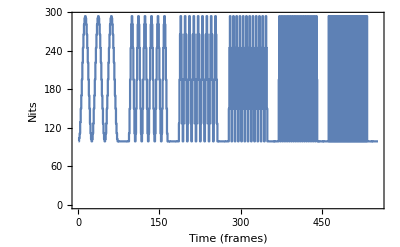

```mathematica
ListStepPlot[vfmtest["luminance"],PlotRange->{0,All},Frame->True,FrameLabel->{"Time (frames)","Nits"}]
```

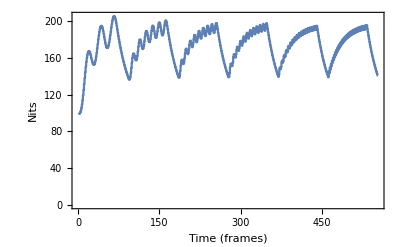

```mathematica
ListStepPlot[vfmtest["adaptationLevel"],PlotRange->{0,All},Frame->True,FrameLabel->{"Time (frames)","Nits"}]
```

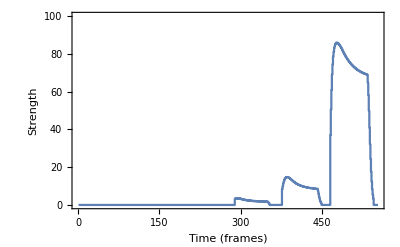

```mathematica
ListStepPlot[vfmtest["risk"],PlotRange->{0,100},Frame->True,FrameLabel->{"Time (frames)","Strength"}]
```

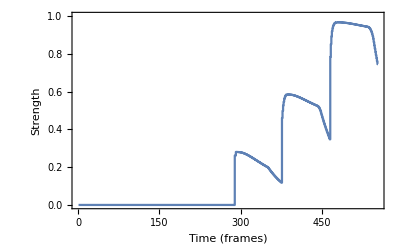

```mathematica
ListStepPlot[vfmtest["mitigationStrength"],PlotRange->{0,1},Frame->True,FrameLabel->{"Time (frames)","Strength"}]
```